# Vaje 4

13. 3. 2025

## 1. kolokvij iz Matematike 1

1. Dokaži, da je za vsako naravno število  izraz  deljiv s .

```mathematica
izraz = 2^(2n+1) - 9n^2 + 3n - 2
izraz /. {n -> 1}
izrazind = izraz /. {n ->  m + 1}
ostanek = (izrazind - (izraz /. {n -> m})) // FullSimplify
indukcija2izraz = ostanek /6
indukcija2izraz /. {m -> 1}
indukcija2izrazKorak = indukcija2izraz /. {m -> k + 1}
ostanek2 = (indukcija2izrazKorak - (indukcija2izraz /. {m -> k})) // FullSimplifyostanek2 = (indukcija2izrazKorak - (indukcija2izraz /. {m -> k})) // FullSimplify
```

-2+2^(1+2 n)+3 n-9 n^2

0

-2+2^(1+2 (1+m))+3 (1+m)-9 (1+m)^2

6 (-1+4^m-3 m)

-1+4^m-3 m

0

-1+4^(1+k)-3 (1+k)

3 (-1+4^k)

2.  Določi vsa realna števila , ki zadoščajo neenačbi .

```mathematica
Reduce[Abs[x^2 + 3x + 2] + Abs[x + 2] > 2*x^2 + x, x]
```

-1<x<4

3. V kompleksnih številih reši enačbo . Rešitve nariši v kompleksni ravnini.

{{z→-ⅈ},{z→ⅈ 3^(1/3)},{z→-(-1)^(1/6) 3^(1/3)},{z→-(-1)^(5/6) 3^(1/3)},{z→1/2 (ⅈ-√3)},{z→1/2 (ⅈ+√3)}}

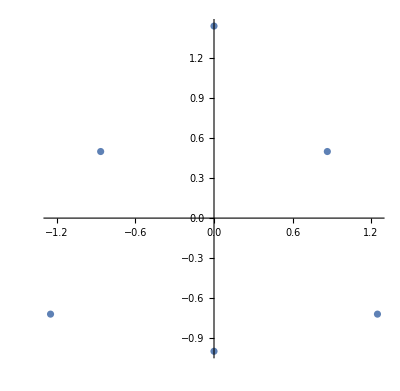

```mathematica
resitev= Solve[Power[z,6] + 2*ⅈ* Power[z,3] + 3 == 0, {z}]
ComplexListPlot[(Flatten[resitev] // Values)]
```

4. Dana je množica . Ugotovi, katere od količin min A, inf A, max A in sup A obstajajo ter jih določi. Vse odgovore natančno utemelji.

```mathematica
(* Izračunamo minimum in maximum funkcije)
```

```mathematica
f[n_]:= (8n + 2)/ (4n -1)
D[f[n], n]// Simplify
(* odvod gre proti nič --> preverimo razliko dveh členov)
```

-16/(1-4 n)^2

```mathematica
f[n]- f[n-1]//FullSimplify
```

-16/(5-24 n+16 n^2)

```mathematica
Limit[f[x],x -> Infinity]
f[1]
```

2

10/3

```mathematica
Solve[f[x]== 2, x]
```

{}

```mathematica
(* min ne obstaja, inf = 2 , max = sup = 10/3
```

## 2. kolokvij iz Matematike 1

1. Funkcija  je podana s predpisom

 
Izračunaj naravno definicijsko območje funkcije  in izračunaj kompozitum , kjer je 

g funkcija, ki je za  enaka , sicer pa je enaka .

```mathematica
f[x_]:= Log[ArcSin[(3+x)/ (3x-1)]]
FunctionDomain[f[x],x]
g[x_]:= Piecewise[{{E^x, x <= Log[Pi/2]}, {E^-x, x > Log[Pi/2]}}]
```

x<-3||x≥2

```mathematica
g[f[x]]// FullSimplify
```

Piecewise[{{1/ArcSin[(3+x)/(-1+3 x)], Log[ArcSin[(3+x)/(-1+3 x)]]>Log[π/2]}, {ArcSin[(3+x)/(-1+3 x)], True}}]

2. Izračunaj naslednjo limito

.

```mathematica
Limit[(n+2)/ (n+1)!^(1/n), n -> Infinity]
```

ⅇ

3. V odvisnosti od  preuči konvergenco zaporednja , ki je podano rekurzivno: , , kjer je  naravno število. V primerih ko zaporedje konvergira, zapiši še njegovo limito.

x

{{x→0},{x→3}}

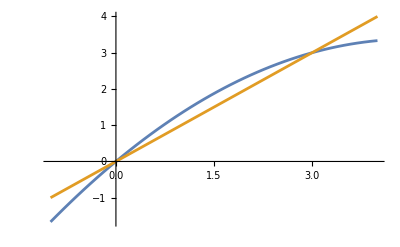

```mathematica
Clear[f,g,x,a]
a[1]= x
a[n_]:= ((9 - a[n - 1])*a[n - 1])/6;
f[x_]:= ((9 - x)x) / 6;
g[x_]:= x;
Solve[f[x] == g[x], {x}]
Plot[{f[x], g[x]}, {x, -1, 4}]
```

4. Poišči vsa realna števila , za katera konvergira vrsta 

.

```mathematica
Clear[n, x]
a[n_]:= Power[x, n]/ (Power[x, 2n] + n)
kvoc = a[n + 1]/ a[n]
```

(x (n+x^(2 n)))/(1+n+x^(2 (1+n)))

```mathematica
Reduce[{Abs[Limit[a[n + 1] / a[n],n -> Infinity]] < 1}, {x}, Reals] (* ni ok *)
```

x>1

```mathematica
a[n] /. {x -> 1}
a[n] /. {x -> -1}
```

1/(1+n)

(-1)^n/((-1)^(2 n)+n)

```mathematica
(* za |x| > 1 vrsta konvergira po kvocientnem kriteriju, za -1 < x < 1 brez 0 konvergira po kvocientnem kriteriju, 
za x = 0 je vsota vrste 0, za x = 1 je harmonična vrsta in divergira, za x = -1 konvergira po Leibnizevem kriteriju *)
```

## 3. kolokvij iz Matematike 1

```mathematica
ClearAll[a, f, x, b]
f[x_] := Piecewise[{
{ArcTan[1/(x*x - 1)], x > 1}, 
{a, x == 1},
{(b Sin[x- 1])/ (x * x - 1), x < 1}
}]
lim1 = Limit[f[x], x -> 1, Direction-> "FromAbove"]
```

π/2

```mathematica
lim2 = a
```

a

```mathematica
lim3 = Limit[f[x], x -> 1, Direction->"FromBelow"]
```

b/2

```mathematica
Solve[ {lim1 == lim2 == lim3}]
```

{{a→π/2,lim3→π/2}}

-Graphics-

```mathematica
ClearAll[x, f, a]
f[x_]:= Sqrt[x^2 + 1]
```

```mathematica
f[1]
```

√2

```mathematica
df= D[f[x], x];
kTangente = df /. {x -> 1}; (* v točki T*)
kNormale = - 1 / kTangente;
normalaT[x_] := kNormale * (x - 1) + f[1];
g[x_] := a - x*x;
```

```mathematica
dg = D[g[x], x];
xDotikalisca  = (Solve[dg == kNormale][[1]] // Values)[[1]]
```

(Piecewise[{{ⅇ^x, x<-Log[2]+Log[π]}, {-ⅇ^-x, x>-Log[2]+Log[π]}, {Indeterminate, True}}])==kNormale

```mathematica
yg = g[xDotikalisca]
```

Piecewise[{{ⅇ^((Piecewise[{{ⅇ^x, x<-Log[2]+Log[π]}, {-ⅇ^-x, x>-Log[2]+Log[π]}, {Indeterminate, True}}])==kNormale), ((Piecewise[{{ⅇ^x, x<-Log[2]+Log[π]}, {-ⅇ^-x, x>-Log[2]+Log[π]}, {Indeterminate, True}}])==kNormale)≤Log[π/2]}, {ⅇ^(-((Piecewise[{{ⅇ^x, x<-Log[2]+Log[π]}, {-ⅇ^-x, x>-Log[2]+Log[π]}, {Indeterminate, True}}])==kNormale)), ((Piecewise[{{ⅇ^x, x<-Log[2]+Log[π]}, {-ⅇ^-x, x>-Log[2]+Log[π]}, {Indeterminate, True}}])==kNormale)>Log[π/2]}, {0, True}}]

```mathematica
normalaT[xDotikalisca]
```

normalaT[(Piecewise[{{ⅇ^x, x<-Log[2]+Log[π]}, {-ⅇ^-x, x>-Log[2]+Log[π]}, {Indeterminate, True}}])==kNormale]

```mathematica
aR = (Solve[yg == normalaT[xDotikalisca], {a}][[1]] // Values)[[1]]
```

{}⟦1⟧

```mathematica
gg[x_] := g[x] /. {a -> aR}
```

```mathematica
Plot[{f[x], gg[x] , normalaT[x]}, {x, 0, 1.1}, PlotLabels->Automatic, AspectRatio->Automatic]
```

-Graphics-

x/(√(1+x^2))

```mathematica
b[a_] := (l - a)/2
```

```mathematica
S[a_ ] := 1/2 * a * Sqrt[Power[b[a], 2] - Power[a, 2]/4]
dS = D[S[a], a]
```

(a (-a/2+(a-l)/2))/(4 √(-a^2/4+1/4 (-a+l)^2))+1/2 √(-a^2/4+1/4 (-a+l)^2)

```mathematica
Solve[dS == 0, {a}]
```

{{a→l/3}}

```mathematica
f[x_]:= (Log[x + 1]) / (x+1)
FunctionDomain[f[x],x]
```

x>-1

```mathematica
FunctionRange[f[x], x, y]
```

y≤1/ⅇ

```mathematica
Reduce[f[x]==0, x]
```

x==0

```mathematica
Limit[f[x], x-> Infinity]
```

0

```mathematica
df = D[f[x], x];
Map[{#, f[#]}&, Solve[df == 0, x] // Flatten // Values]
```

{{-1+ⅇ,1/ⅇ}}

```mathematica
ddf = D[f[x], {x, 2}] ;
ddf /. {x -> -1 + E}
```

-1/ⅇ^3

```mathematica
Reduce[df >= 0, x]
```

-1<x≤-1+ⅇ

```mathematica
Reduce[df <= 0, x]
```

x≥-1+ⅇ

```mathematica
Reduce[ddf == 0, x]
```

x==-1+ⅇ^(3/2)

```mathematica
Reduce[ddf >= 0, x] (* konveksno *)
Reduce[ddf <= 0, x] (* konkavno *)
```

x≥-1+ⅇ^(3/2)

```mathematica
-1<x≤-1+ⅇ^(3/2)
Plot[f[x], {x, -1, 4}, PlotLabels->Automatic]
```

-1<x≤-1+ⅇ^(3/2)

-Graphics-